```mathematica
(*  F[1, {1}] = electron neutrino, F[1, {2}] = muon neutrino, F[1, {3}] = tau neutrino, 
	F[2, {1}] = electron, F[2, {2}] = muon, F[2, {3}] = tau,  
	F[3, {1}] = up, F[3, {2}] = charm, F[3, {3}] = top,  
	F[4, {1}] = down, F[4, {2}] = strange, F[4, {3}] = bottom, 
	V[1] = photon, V[2] = Z, V[3] = W-, S[1] = H *)
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;

MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
topology = CreateTopologies[0,1->3];
```

FeynCalc 10.0.0 (dev version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

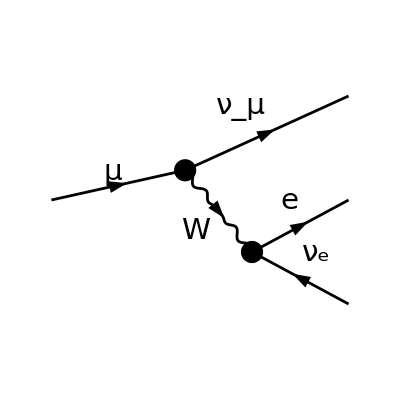

-(2 √2 G_F m_W^2 (φ(OverBar[p_2],m_e)).(γ̄)^Lor2.(γ̄)^7.(φ(-OverBar[p_3])) (φ(OverBar[p_1])).(γ̄)^Lor2.(γ̄)^7.(φ(p̄,m_μ)))/((OverBar[p_2]+OverBar[p_3])^2-m_W^2)-(2 √2 G_F (φ(OverBar[p_2],m_e)).(γ̄·(OverBar[p_2]+OverBar[p_3])).(γ̄)^7.(φ(-OverBar[p_3])) (φ(OverBar[p_1])).(γ̄·(-OverBar[p_2]-OverBar[p_3])).(γ̄)^7.(φ(p̄,m_μ)))/((OverBar[p_2]+OverBar[p_3])^2-m_W^2)

16 G_F^2 (1/((OverBar[p_2]+OverBar[p_3])^2-m_W^2))^2 (-2 m_e^2 (p̄·OverBar[p_1]) (OverBar[p_2]·OverBar[p_3])^2-2 m_e^2 m_W^2 (p̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_2])-2 m_e^2 m_W^2 (p̄·OverBar[p_2]) (OverBar[p_1]·OverBar[p_3])+2 m_e^2 m_W^2 (p̄·OverBar[p_1]) (OverBar[p_2]·OverBar[p_3])+m_e^4 (-(p̄·OverBar[p_1])) (OverBar[p_2]·OverBar[p_3])+2 m_e^2 (p̄·OverBar[p_2]) (OverBar[p_1]·OverBar[p_2]) (OverBar[p_2]·OverBar[p_3])+2 m_e^2 (p̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_2]) (OverBar[p_2]·OverBar[p_3])+2 m_e^2 (p̄·OverBar[p_2]) (OverBar[p_1]·OverBar[p_3]) (OverBar[p_2]·OverBar[p_3])+2 m_e^2 (p̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_3]) (OverBar[p_2]·OverBar[p_3])-4 m_e^2 m_W^2 (p̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_3])+4 m_W^4 (p̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_2]))

64 G_F^2 (p̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_2])

```mathematica
(* SM: mu -> nu_mu e- antinu_e *)
feynman=InsertFields[topology, {F[2,{2}]}->{F[1,{2}],F[2,{1}], -F[1,{1}]}, InsertionLevel->{Classes},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman, GaugeRules->{FAGaugeXi[W|Z]->Infinity}],IncomingMomenta->{p},OutgoingMomenta->{p1,p2, p3},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True, DropSumOver->True,FinalSubstitutions->{SMP["e"]->Sqrt[8/Sqrt[2]*SMP["G_F"]*SMP["m_W"]^2 SMP["sin_W"]^2]}]
FCClearScalarProducts[];
SP[p,p]=SMP["m_mu"]^2;
SP[p1,p1]=0;
SP[p2,p2]=SMP["m_e"]^2;
SP[p3,p3]=0;
squareamplitude[0]=(amplitude[0] (ComplexConjugate[amplitude[0]]))//FermionSpinSum[#,ExtraFactor->1/2]&//DiracSimplify//Factor
squareamplitude[1]=squareamplitude[0]//FCE//ReplaceAll[#,{p2+p3->0}]&//FeynAmpDenominatorExplicit//Series[#,{SMP["m_W"],Infinity,0}]&//Normal
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

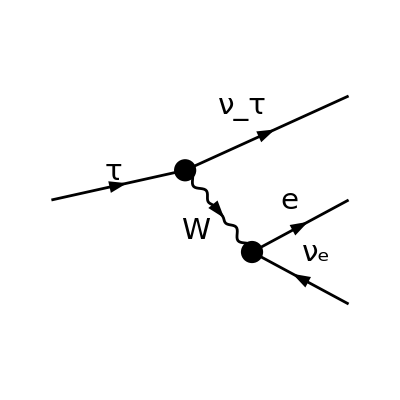

-(2 √2 G_F m_W^2 (φ(OverBar[p_2],m_e)).(γ̄)^Lor2.(γ̄)^7.(φ(-OverBar[p_3])) (φ(OverBar[p_1])).(γ̄)^Lor2.(γ̄)^7.(φ(p̄,m_τ)))/((OverBar[p_2]+OverBar[p_3])^2-m_W^2)-(2 √2 G_F (φ(OverBar[p_2],m_e)).(γ̄·(OverBar[p_2]+OverBar[p_3])).(γ̄)^7.(φ(-OverBar[p_3])) (φ(OverBar[p_1])).(γ̄·(-OverBar[p_2]-OverBar[p_3])).(γ̄)^7.(φ(p̄,m_τ)))/((OverBar[p_2]+OverBar[p_3])^2-m_W^2)

16 G_F^2 (1/((OverBar[p_2]+OverBar[p_3])^2-m_W^2))^2 (-2 m_e^2 (p̄·OverBar[p_1]) (OverBar[p_2]·OverBar[p_3])^2-2 m_e^2 m_W^2 (p̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_2])-2 m_e^2 m_W^2 (p̄·OverBar[p_2]) (OverBar[p_1]·OverBar[p_3])+2 m_e^2 m_W^2 (p̄·OverBar[p_1]) (OverBar[p_2]·OverBar[p_3])+m_e^4 (-(p̄·OverBar[p_1])) (OverBar[p_2]·OverBar[p_3])+2 m_e^2 (p̄·OverBar[p_2]) (OverBar[p_1]·OverBar[p_2]) (OverBar[p_2]·OverBar[p_3])+2 m_e^2 (p̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_2]) (OverBar[p_2]·OverBar[p_3])+2 m_e^2 (p̄·OverBar[p_2]) (OverBar[p_1]·OverBar[p_3]) (OverBar[p_2]·OverBar[p_3])+2 m_e^2 (p̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_3]) (OverBar[p_2]·OverBar[p_3])-4 m_e^2 m_W^2 (p̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_3])+4 m_W^4 (p̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_2]))

64 G_F^2 (p̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_2])

```mathematica
(* SM: tau -> nu_tau e- antinu_e *)
feynman=InsertFields[topology, {F[2,{3}]}->{F[1,{3}],F[2,{1}], -F[1,{1}]}, InsertionLevel->{Classes},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman, GaugeRules->{FAGaugeXi[W|Z]->Infinity}],IncomingMomenta->{p},OutgoingMomenta->{p1,p2, p3},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True, DropSumOver->True,FinalSubstitutions->{SMP["e"]->Sqrt[8/Sqrt[2]*SMP["G_F"]*SMP["m_W"]^2 SMP["sin_W"]^2]}]
FCClearScalarProducts[];
SP[p,p]=SMP["m_tau"]^2;
SP[p1,p1]=0;
SP[p2,p2]=SMP["m_e"]^2;
SP[p3,p3]=0;
squareamplitude[0]=(amplitude[0] (ComplexConjugate[amplitude[0]]))//FermionSpinSum[#,ExtraFactor->1/2]&//DiracSimplify//Factor
squareamplitude[1]=squareamplitude[0]//FCE//ReplaceAll[#,{p2+p3->0}]&//FeynAmpDenominatorExplicit//Series[#,{SMP["m_W"],Infinity,0}]&//Normal
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

```mathematica
topology = CreateTopologies[0,1->2];
```

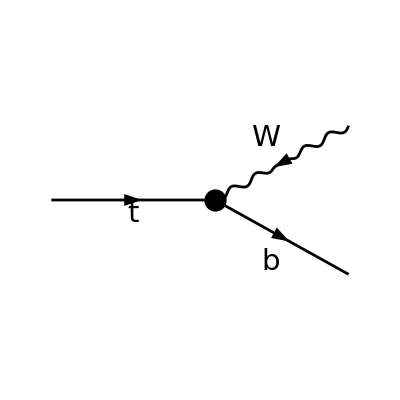

(2^(3/4) δ_Col1Col3 √(G_F m_W^2 (sin(θ_W))^2) (φ(OverBar[p_2],m_b)).(γ̄·(ε̄)^*(p_1)).(γ̄)^7.(φ(p̄,m_t)))/(sin(θ_W))

√2 C_A G_F (-2 m_b^2 m_τ^2+m_b^2 m_W^2+m_b^4+m_τ^4+m_τ^2 m_W^2-2 m_W^4)

√2 C_A G_F (m_τ^4+m_τ^2 m_W^2-2 m_W^4)

```mathematica
(* SM: t -> W+ b *)
feynman=InsertFields[topology, {F[3,{3}]}->{-V[3],F[4,{3}]}, InsertionLevel->{Classes},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman],IncomingMomenta->{p},OutgoingMomenta->{p1,p2},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True, DropSumOver->True,FinalSubstitutions->{SMP["e"]->Sqrt[8/Sqrt[2]*SMP["G_F"]*SMP["m_W"]^2 SMP["sin_W"]^2]}]
FCClearScalarProducts[];
SP[p,p]=SMP["m_tau"]^2;
SP[p1,p1]=SMP["m_W"]^2;
SP[p2,p2]=SMP["m_b"]^2;
SP[p1,p2]=(SMP["m_tau"]^2-SMP["m_W"]^2 -SMP["m_b"]^2)/2;
SP[p,p1]= SP[p1,p1] + SP[p1,p2];
SP[p,p2]=SP[p1,p2] + SP[p2,p2];
squareamplitude[0]=(amplitude[0] (ComplexConjugate[amplitude[0]])) //DoPolarizationSums[#,p1] &//FermionSpinSum[#,ExtraFactor->1/2] &//DiracSimplify//Simplify //SUNSimplify
masslesssquareamplitude[0] = squareamplitude[0]//ReplaceAll[#,{SMP["m_b"]->0}]&//Simplify 
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

```mathematica
Print["\tCPU Time used: ",Round[N[TimeUsed[],4],0.001]," s."];
```

CPU Time used: 3.94 s.

```mathematica
FeynCalcHowToCite[]
```

• V. Shtabovenko, R. Mertig and F. Orellana, arXiv:2312.14089.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

Null